# Texas Sharpshooter

```mathematica
pts=BlockRandom[RandomReal[{-1,1},{8,2}],RandomSeeding->1];
```

```mathematica
RegionFit[pts,"Circle"]
```

Circle[{0.465382,0.0958824},0.73925]

```mathematica
Subsets[pts,{3}]
```

{{{0.634779,-0.777161},{0.579052,-0.624394},{-0.517278,-0.868522}},{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691}},{{0.634779,-0.777161},{0.579052,-0.624394},{-0.207988,0.400948}},{{0.634779,-0.777161},{0.579052,-0.624394},{-0.576348,0.497314}},{{0.634779,-0.777161},{0.579052,-0.624394},{-0.154299,-0.50501}},{{0.634779,-0.777161},{0.579052,-0.624394},{0.954344,0.650326}},{{0.634779,-0.777161},{-0.517278,-0.868522},{0.0844932,-0.537691}},{{0.634779,-0.777161},{-0.517278,-0.868522},{-0.207988,0.400948}},{{0.634779,-0.777161},{-0.517278,-0.868522},{-0.576348,0.497314}},{{0.634779,-0.777161},{-0.517278,-0.868522},{-0.154299,-0.50501}},{{0.634779,-0.777161},{-0.517278,-0.868522},{0.954344,0.650326}},{{0.634779,-0.777161},{0.0844932,-0.537691},{-0.207988,0.400948}},{{0.634779,-0.777161},{0.0844932,-0.537691},{-0.576348,0.497314}},{{0.634779,-0.777161},{0.0844932,-0.537691},{-0.154299,-0.50501}},{{0.634779,-0.777161},{0.0844932,-0.537691},{0.954344,0.650326}},{{0.634779,-0.777161},{-0.207988,0.400948},{-0.576348,0.497314}},{{0.634779,-0.777161},{-0.207988,0.400948},{-0.154299,-0.50501}},{{0.634779,-0.777161},{-0.207988,0.400948},{0.954344,0.650326}},{{0.634779,-0.777161},{-0.576348,0.497314},{-0.154299,-0.50501}},{{0.634779,-0.777161},{-0.576348,0.497314},{0.954344,0.650326}},{{0.634779,-0.777161},{-0.154299,-0.50501},{0.954344,0.650326}},{{0.579052,-0.624394},{-0.517278,-0.868522},{0.0844932,-0.537691}},{{0.579052,-0.624394},{-0.517278,-0.868522},{-0.207988,0.400948}},{{0.579052,-0.624394},{-0.517278,-0.868522},{-0.576348,0.497314}},{{0.579052,-0.624394},{-0.517278,-0.868522},{-0.154299,-0.50501}},{{0.579052,-0.624394},{-0.517278,-0.868522},{0.954344,0.650326}},{{0.579052,-0.624394},{0.0844932,-0.537691},{-0.207988,0.400948}},{{0.579052,-0.624394},{0.0844932,-0.537691},{-0.576348,0.497314}},{{0.579052,-0.624394},{0.0844932,-0.537691},{-0.154299,-0.50501}},{{0.579052,-0.624394},{0.0844932,-0.537691},{0.954344,0.650326}},{{0.579052,-0.624394},{-0.207988,0.400948},{-0.576348,0.497314}},{{0.579052,-0.624394},{-0.207988,0.400948},{-0.154299,-0.50501}},{{0.579052,-0.624394},{-0.207988,0.400948},{0.954344,0.650326}},{{0.579052,-0.624394},{-0.576348,0.497314},{-0.154299,-0.50501}},{{0.579052,-0.624394},{-0.576348,0.497314},{0.954344,0.650326}},{{0.579052,-0.624394},{-0.154299,-0.50501},{0.954344,0.650326}},{{-0.517278,-0.868522},{0.0844932,-0.537691},{-0.207988,0.400948}},{{-0.517278,-0.868522},{0.0844932,-0.537691},{-0.576348,0.497314}},{{-0.517278,-0.868522},{0.0844932,-0.537691},{-0.154299,-0.50501}},{{-0.517278,-0.868522},{0.0844932,-0.537691},{0.954344,0.650326}},{{-0.517278,-0.868522},{-0.207988,0.400948},{-0.576348,0.497314}},{{-0.517278,-0.868522},{-0.207988,0.400948},{-0.154299,-0.50501}},{{-0.517278,-0.868522},{-0.207988,0.400948},{0.954344,0.650326}},{{-0.517278,-0.868522},{-0.576348,0.497314},{-0.154299,-0.50501}},{{-0.517278,-0.868522},{-0.576348,0.497314},{0.954344,0.650326}},{{-0.517278,-0.868522},{-0.154299,-0.50501},{0.954344,0.650326}},{{0.0844932,-0.537691},{-0.207988,0.400948},{-0.576348,0.497314}},{{0.0844932,-0.537691},{-0.207988,0.400948},{-0.154299,-0.50501}},{{0.0844932,-0.537691},{-0.207988,0.400948},{0.954344,0.650326}},{{0.0844932,-0.537691},{-0.576348,0.497314},{-0.154299,-0.50501}},{{0.0844932,-0.537691},{-0.576348,0.497314},{0.954344,0.650326}},{{0.0844932,-0.537691},{-0.154299,-0.50501},{0.954344,0.650326}},{{-0.207988,0.400948},{-0.576348,0.497314},{-0.154299,-0.50501}},{{-0.207988,0.400948},{-0.576348,0.497314},{0.954344,0.650326}},{{-0.207988,0.400948},{-0.154299,-0.50501},{0.954344,0.650326}},{{-0.576348,0.497314},{-0.154299,-0.50501},{0.954344,0.650326}}}

```mathematica
RegionFit[pts,"Circle"]
```

Circle[{0.465382,0.0958824},0.73925]

```mathematica
Disk@@RegionFit[pts,"Circle"]
```

Disk[{0.465382,0.0958824},0.73925]

```mathematica
Area[Disk@@RegionFit[pts,"Circle"]]
```

1.71685

```mathematica
MinimalBy[Area[Disk@@RegionFit[#,"Circle"]]&][Subsets[pts,{3}]]
```

{{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691}}}

```mathematica
MinimalBy[Area[Disk@@RegionFit[#,"Circle"]]&][Subsets[pts,{3}]]
```

{{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691}}}

```mathematica
MinimalBy[Area[Disk@@RegionFit[#,"Circle"]]&][Subsets[pts,{2,8}]]
```

RegionFit::argtu: RegionFit called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of RegionFit::argtu will be suppressed during this calculation.

{{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691}},{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691},{-0.207988,0.400948}},{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691},{-0.576348,0.497314}},{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691},{-0.154299,-0.50501}},{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691},{0.954344,0.650326}},{{0.634779,-0.777161},{0.579052,-0.624394},{-0.517278,-0.868522},{0.0844932,-0.537691},{-0.207988,0.400948}},{{0.634779,-0.777161},{0.579052,-0.624394},{-0.517278,-0.868522},{0.0844932,-0.537691},{-0.576348,0.497314}},{{0.634779,-0.777161},{0.579052,-0.624394},{-0.517278,-0.868522},{0.0844932,-0.537691},{-0.154299,-0.50501}},{{0.634779,-0.777161},{0.579052,-0.624394},{-0.517278,-0.868522},{0.0844932,-0.537691},{0.954344,0.650326}}}

```mathematica
RegionFit[First@MinimalBy[Area[Disk@@RegionFit[#,"Circle"]]&][Subsets[pts,{2,8}]],"Circle"]
```

RegionFit::argtu: RegionFit called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of RegionFit::argtu will be suppressed during this calculation.

Circle[{0.290549,-0.816183},0.346434]

## Ideas

I think I need to use BoundingRegion because it allows the points to be contained within not RegionFit which tries to fit the points on the circle.

```mathematica
pts={{3,10},{6,3},{10,2},{2,8},{3,3}};
```

```mathematica
BoundingRegion[pts,"MinDisk"]
```

Disk[{13/2,6},(√113)/2]

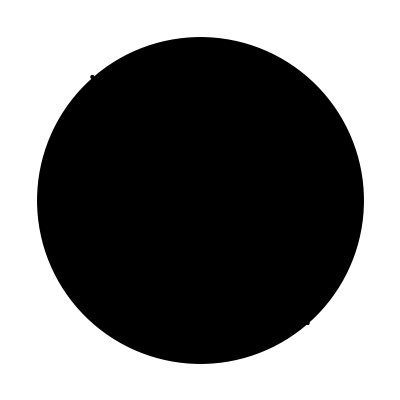

```mathematica
Region[%,Epilog->{Black,Point[pts]}]
```

```mathematica
AssociationMap[RegionFit[pts,"Circle",#]&,{"BestFit","Points","Inliers","Outliers","DistanceVariance","Distances"}]
```

<|BestFit→Circle[{159/26,187/26},(√(5945/2))/13],Points→{{3,10},{6,3},{10,2},{2,8},{3,3}},Inliers→{{3,10},{6,3},{2,8}},Outliers→{{10,2},{3,3}},DistanceVariance→1/4 (3/25 ((√(9221/2))/13+(√(14213/2))/13-(√11890)/13)^2+(-(√(5945/2))/13+(√(9221/2))/13+1/5 (-(√(9221/2))/13-(√(14213/2))/13+(√11890)/13))^2+(-(√(5945/2))/13+(√(14213/2))/13+1/5 (-(√(9221/2))/13-(√(14213/2))/13+(√11890)/13))^2),Distances→{0,0,-(√(5945/2))/13+(√(14213/2))/13,0,-(√(5945/2))/13+(√(9221/2))/13}|>

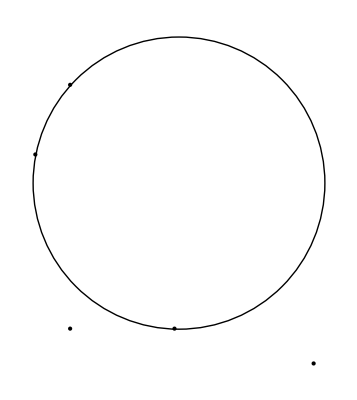

```mathematica
Graphics[{RegionFit[pts,"Circle"],Point[pts]}]
```

```mathematica
pts=BlockRandom[RandomReal[{-1,1},{8,2}],RandomSeeding->1]
```

{{0.634779,-0.777161},{0.579052,-0.624394},{-0.517278,-0.868522},{0.0844932,-0.537691},{-0.207988,0.400948},{-0.576348,0.497314},{-0.154299,-0.50501},{0.954344,0.650326}}

How many points are there?

```mathematica
Length[pts]
```

8

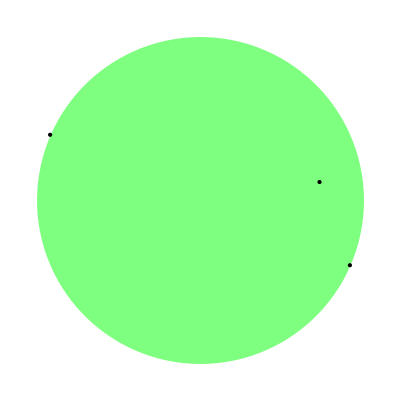

```mathematica
Graphics[{Style[Disk[{0.359636,-0.657426},0.300067],Directive[Opacity[0.5],Green]]},Epilog->{Black,Point[pts]}]
```

Which points are in the output disk?

```mathematica
pointsindisk=Select[RegionMember[Disk[{0.359636,-0.657426},0.300067],#]&][pts]
```

{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691}}

```mathematica
Position[pointsindisk][Subsets[pts,{3}]]
```

{{2}}

```mathematica
BoundingRegion[pointsindisk,"MinDisk"]
```

Disk[{0.359636,-0.657426},0.300067]

```mathematica
Area[BoundingRegion[pointsindisk,"MinDisk"]]
```

0.282869

```mathematica
TakeSmallestBy[Area[BoundingRegion[#,"MinDisk"]]&,1][Subsets[pts,{3}]]
```

{{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691}}}

```mathematica
TakeSmallestBy[Area,1][AssociationMap[BoundingRegion[#,"MinDisk"]&][Subsets[pts,{3}]]]
```

<|{{0.634779,-0.777161},{0.579052,-0.624394},{0.0844932,-0.537691}}→Disk[{0.359636,-0.657426},0.300067]|>

```mathematica
Values[TakeSmallestBy[Area,1][AssociationMap[BoundingRegion[#,"MinDisk"]&][Subsets[pts,{3}]]]]
```

{Disk[{0.359636,-0.657426},0.300067]}

```mathematica
Sharpshooter[pts_?MatrixQ]:=First[Values[TakeSmallestBy[Area,1][AssociationMap[BoundingRegion[#,"MinDisk"]&][Subsets[pts,{3}]]]]]
```

## Testing the Function

```mathematica
pts=BlockRandom[RandomReal[{-1,1},{8,2}],RandomSeeding->10];
```

```mathematica
Sharpshooter[pts]
```

Disk[{0.0425318,0.368225},0.419213]

```mathematica
pts=BlockRandom[RandomReal[{-1,1},{8,2}],RandomSeeding->100];
```

```mathematica
Sharpshooter[pts]
```

Disk[{0.533105,-0.38852},0.350359]

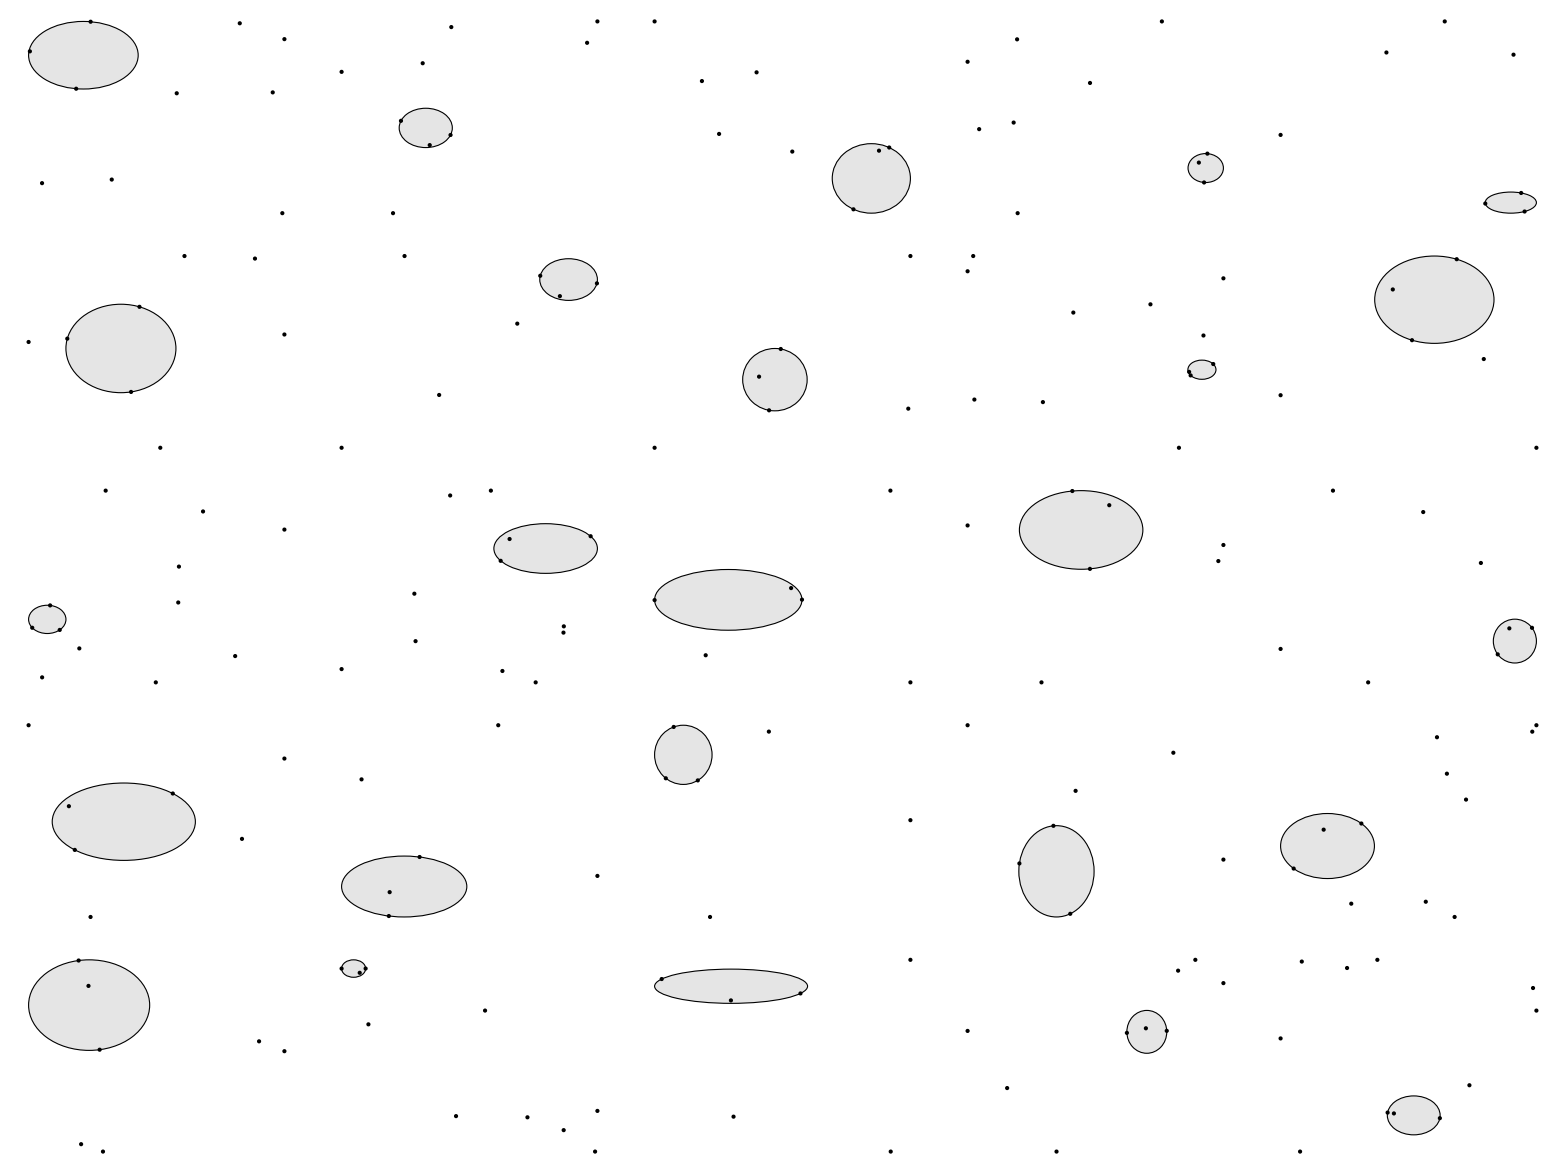

```mathematica
Multicolumn[Table[With[{rand=RandomReal[{-1,1},{RandomInteger[{6,12}],2}]},Graphics[{EdgeForm[Black],{Opacity[.1],Sharpshooter[rand]},Point[rand]},ImageSize->{100,100}]],25],Frame->All]
```

Performance Statistics